```mathematica
(*Import the video and set videoFrames to the image list of frames *)

filename="D:\\OU Fall 2023\\Advnaced Lab lets GO!\\Cavendish\\runs\\run1.MOV";
frames=Import[filename,"ImageList"];
```

```mathematica
(*Get video dimensions for cropping*)
```

```mathematica
Manipulate[ImageTake[videoFrames[[1]],{a,b},{c,d}],{a,1,1080},{b,2,1080},{c,1,1920},{d,2,1920}]
```

Part::partd: Part specification videoFrames⟦1⟧ is longer than depth of object.

ImageTake::imginv: Expecting an image or graphics instead of videoFrames⟦1⟧.

Part::partd: Part specification videoFrames⟦1⟧ is longer than depth of object.

ImageTake::imginv: Expecting an image or graphics instead of videoFrames⟦1⟧.

```mathematica
(*Cropping the image *)
length=Length[frames];
ymin=230;
ymax=370;
xmin=1;
xmax=1920;
croppedFrames=Table[ImageTake[frames[[i]],{ymin,ymax},{xmin,xmax}],{i,length}];
```

```mathematica
(*Show crop*)
```

```mathematica
croppedFrames[[1]]
```

-Graphics-

```mathematica
length
```

714

```mathematica
(*Use binarize to create a binary image set*)
```

```mathematica
binarizedFrames=Table[Binarize[croppedFrames[[i]],.5],{i,length}];
newBinarizedFrames=Table[DeleteSmallComponents[binarizedFrames[[i]]],{i,length}];
```

```mathematica
(*Get coordinates for the pixels*)
```

```mathematica
help=Table[ComponentMeasurements[newBinarizedFrames[[i]],"Centroid"],{i,length}]//Values;
xvals=Flatten[help[[;;,;;,1]]];
yvals=Flatten[help[[;;,;;,2]]];
```

```mathematica
(*Plot*)
```

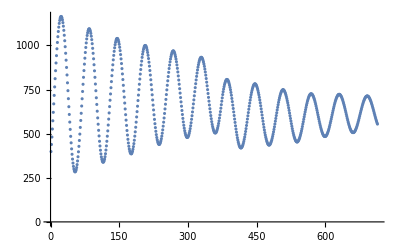

```mathematica
ListPlot[Transpose[xvals]]
```